## Camera resolution tests

## setup

```mathematica
imagedir=FileNameJoin[{NotebookDirectory[],"resolution_tests\\"}];
AppendTo[$Path, imagedir];
USAFlpmm[group_,element_]:=2^(group+(element-1)/6)//N; (*gives line pairs per mm on a USAF standard, where line pair is defined to be a bright and dark line*)
```

## Rb Andor iXon

```mathematica
img = Import["usaf_1951_rb_andor_ixon_20210511_gray.tif"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

64

64

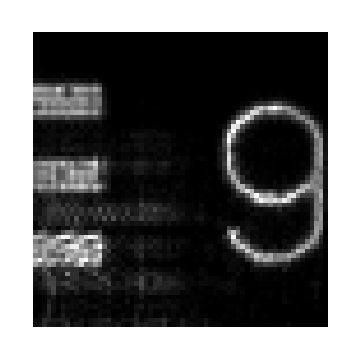

```mathematica
Show[Image[data],ImageSize->Medium]
```

```mathematica
Image[data[[1;;64,1;;15]],ImageSize->Medium]
```

-Graphics-

{μ→15.53,a→8.10358,σ→2.73271}

pixels per μm in object plane= 3.696

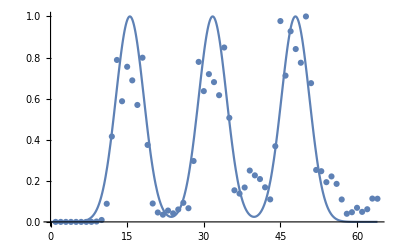

```mathematica
group=7;
elem=6;
rowAvg=Sum[data[[1;;64,i]],{i,1,15}];
rowAvg/=Max[rowAvg];
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,15},{a,10},σ},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,64}],PlotRange-> All]
```

## Urban camera

As of 2021.03, the Urban camera CCD has been replaced with a PointGrey CCD. These are the resolution tests performed with a USAF 1951 1x standard for various wavelengths.

```mathematica
{{"Wavelength", "Pixels/μm", "Date"}, {650, 12.37, 2021/3/15}, {780, 12.12, 2021/3/15}, {852, 12.02, 2021/3/15}}
```

### 650

```mathematica
img = ColorConvert[Import["urban_camera_650_fault_finder_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[280;;380,60;;220]]](*7,6 using this*)
```

-Graphics-

```mathematica
Image[data[[290;;410,280;;480]]](*7,5*)
```

-Graphics-

```mathematica
group=7;
elem=6;
```

```mathematica
rowAvg=Sum[data[[i,60;;220]],{i,280,380}];
rowAvg/=Max[rowAvg];
```

{μ→32.3185,a→27.1156,σ→4.96391}

pixels per μm in object plane= 12.37

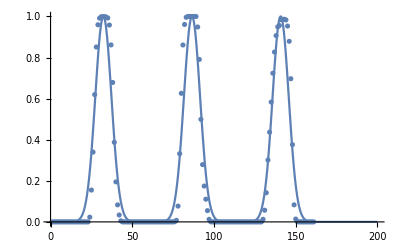

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,30},{a,30},σ},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```

### 780

```mathematica
img = ColorConvert[Import["urban_camera_780_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[290;;400,100;;280]]](*7,6*)
```

-Graphics-

```mathematica
Image[data[[280;;390,280;;480]]](*7,5 using this because more uniform than 7,6*)
```

-Graphics-

```mathematica
group=7;
elem=5;
```

```mathematica
rowAvg=Sum[data[[i,280;;480]],{i,280,390}];
rowAvg/=Max[rowAvg];
```

{μ→35.6998,a→29.837,σ→14.6021}

pixels per μm in object plane= 12.12

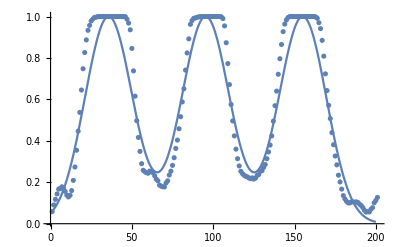

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,40},{a,35},{σ,10}},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```

### 852

```mathematica
img = ColorConvert[Import["urban_camera_852_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
leny
```

1280

```mathematica
Image[data[[290;;400,100;;280]]](*7,6*)
```

-Graphics-

```mathematica
Image[data[[290;;410,280;;480]]](*6,6. using this rather than 7,6 because more uniform line-to-line*)
```

-Graphics-

```mathematica
group=7;
elem=5;
```

```mathematica
rowAvg=Sum[data[[i,280;;480]],{i,290,410}];
rowAvg/=Max[rowAvg];
```

{μ→42.1142,a→29.5782,σ→10.1447}

pixels per μm in object plane= 12.02

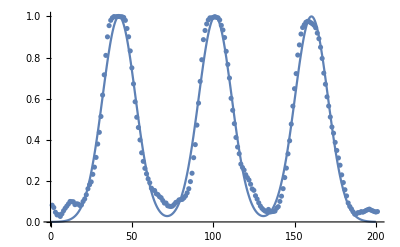

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,40},{a,35},{σ,10}},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```

## microscope for parabolic mirror characterization

The homemade long-working distance high NA microscope made from a 0.7 NA asphere at 780 nm (BFL 24 mm), a 1 m FL plano-convex lens, and a Thorlabs CS165MU1. The microscopy standard is from Technologie Manufaktur, sold by Edmund.

```mathematica
0.001/160
```

6.25×10^-6

### 2022.09.12

fiber face under the microscope

```mathematica
img=-Graphics-;
```

```mathematica
ImageData[img]//Dimensions
```

{1080,1440}

```mathematica
data=ImageData[img];
```

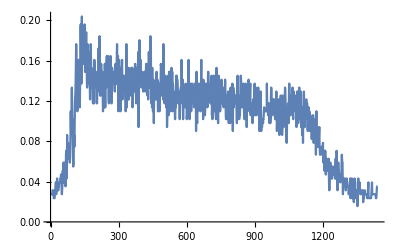

```mathematica
ListPlot[data[[502,;;]],Joined->True]
```

```mathematica
(*width is about 1100 pixels*)
"actual magnification"
am=(1100*3.45)/125
"expected magnification"
em=996/32//N
```

actual magnification

30.36

expected magnification

31.125

### 2022.08.10

```mathematica
img=-Graphics-;
img
```

-Graphics-

```mathematica
data=ImageData[img];
```

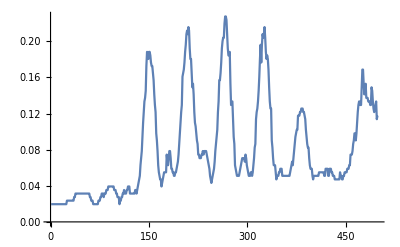

```mathematica
ListPlot[data[[487,;;498]],Joined->True,PlotRange->All]
```

```mathematica
1/160//N
```

0.00625

2 micron pinhole

```mathematica
img=-Graphics-;
data=ImageData[img];
```

```mathematica
data//Dimensions
```

{413,424,3}

```mathematica
img=ColorConvert[img,"grayscale"]
```

-Graphics-

```mathematica
data=GaussianFilter[ImageData[img][[20;;390,20;;390]],10];(*//Dimensions*)
filtered=GaussianFilter[data,10];
filtered-=Min[filtered];
ListPlot3D[filtered/Max[filtered],PlotRange->All]
ListPlot3D[data,PlotRange->All]
```

-Graphics3D-

```mathematica
x0=20;
Plot3D[BesselJ[1,√(x^2+y^2)]/(√(x^2+y^2)),{x,-x0,x0},{y,-x0,x0},PlotRange->All,PerformanceGoal->"Quality",PlotPoints->50]
```

-Graphics3D-

```mathematica
Max[data]
```

1.

```mathematica
ListPlot3D[data,PlotRange->{{20,390},{20,390},{0,0.3}}]
```

-Graphics3D-

Transpose::nonopt: Options expected (instead of {{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},«414»}) beyond position 2 in Transpose[«1»,{{0.129412,0.129412,0.129412},{0.129412,0.129412,0.129412},{0.12549,0.12549,0.12549},{0.117647,0.117647,0.117647},{0.113725,«20»,«20»},{«1»},{«1»},{0.121569,0.121569,0.121569},{0.121569,0.121569,0.121569},{0.121569,0.121569,0.121569},«414»},«8»,«403»]. An option must be a rule or a list of rules.

{413}

```mathematica
(*1 um diameter pinhole*)
```

```mathematica
img=-Graphics-;
img=ColorConvert[img,"grayscale"];
```

```mathematica
data=1-ImageData[img][[200;;400,400;;600]];
(*Image[data[[200;;400,400;;600]]];*)
ListPlot3D[data,PlotRange->All]
filtered=GaussianFilter[data,10];
filtered-=Min[filtered];
ListPlot3D[filtered/Max[filtered],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
data//Dimensions
```

{201,201}

```mathematica
max=Max[filtered];
For[i=1,i<202,i++,
For[j=1,j<202,j++,
If[filtered[[i,j]]==max,
Print[i," ",j];
Break[]]
]
]
```

108 99

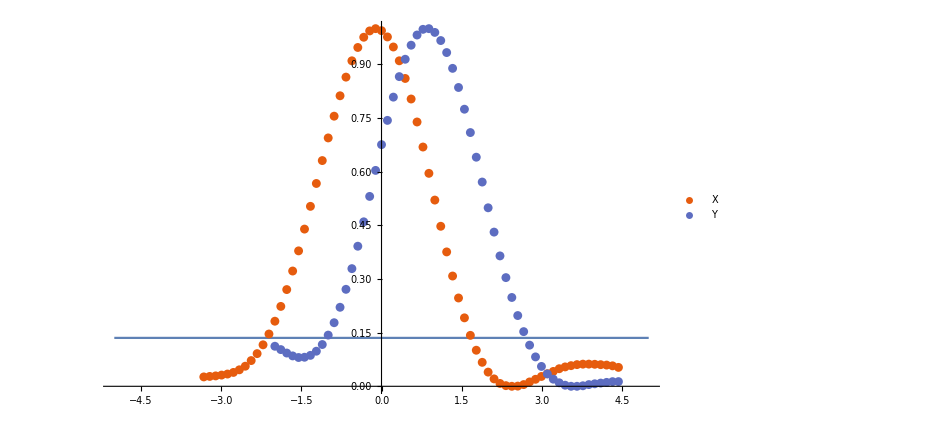

```mathematica
m=996/32;
maxIdx=40;
minIdx=30;
xlist=Range[-minIdx,maxIdx]*3.45/m;
xclipped=(filtered[[108]][[100-minIdx;;100+maxIdx]])/max;
xclipped-=Min[xclipped];
xclipped/=Max[xclipped];
maxIdx=40;
minIdx=18;
ylist=Range[-minIdx,maxIdx]*3.45/m;
yclipped=(filtered[[;;,99]][[100-minIdx;;100+maxIdx]])/max;
yclipped-=Min[yclipped];
yclipped/=Max[yclipped];
xdata=Transpose@{xlist,xclipped};
ydata=Transpose@{ylist,yclipped};
Show[Plot[1/E^2,{x,-5,5}],ListPlot[{xdata,ydata},PlotTheme->"Scientific",FrameLabel->{"μm in object space"},PlotLegends->{"X","Y"}],PlotRange->{0,1}]
```

```mathematica
yinterp=Interpolation[ydata];
xinterp=Interpolation[xdata];
```

```mathematica
NSolve[yinterp[u]==1/E^2,u,Reals]
```

NSolve[InterpolatingFunction[…][u]==1/ⅇ^2,u,ℝ]

1 um pinhole, after making slight (questionable) improvements to the microscope alignment

```mathematica
img=-Graphics-;
```

```mathematica
Image[ImageData[img][[648-100;;648+100,685-100;;685+100]]]
```

-Graphics-

```mathematica
data=ImageData[img][[648-100;;648+100,685-100;;685+100]];
ListPlot3D[data,PlotRange->All]
filtered=GaussianFilter[data,10];
filtered-=Min[filtered];
ListPlot3D[filtered/Max[filtered],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
max=Max[filtered];
For[i=1,i<202,i++,
For[j=1,j<202,j++,
If[filtered[[i,j]]==max,
Print[i," ",j];
xmax=i;
ymax=j;
Break[]]
]
]
```

101 102

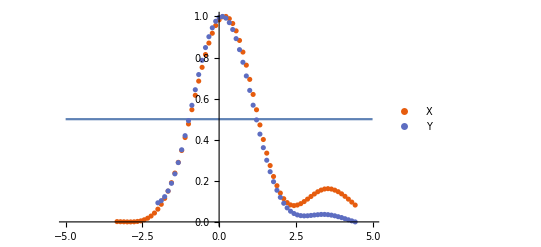

```mathematica
m=996/32;
maxIdx=40;
minIdx=30;
xlist=Range[-minIdx,maxIdx]*3.45/m;
xclipped=(filtered[[xmax]][[100-minIdx;;100+maxIdx]])/max;
xclipped-=Min[xclipped];
xclipped/=Max[xclipped];
maxIdx=40;
minIdx=18;
ylist=Range[-minIdx,maxIdx]*3.45/m;
yclipped=(filtered[[;;,ymax]][[100-minIdx;;100+maxIdx]])/max;
yclipped-=Min[yclipped];
yclipped/=Max[yclipped];
xdata=Transpose@{xlist,xclipped};
ydata=Transpose@{ylist,yclipped};
Show[Plot[1/2,{x,-5,5}],ListPlot[{xdata,ydata},PlotTheme->"Scientific",FrameLabel->{"μm in object space"},PlotLegends->{"X","Y"}],PlotRange->{0,1}]
```